# EIWL Sections 47 and 48

## 8/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

```mathematica
Total[#*(# + 1)&/@Range[1000]]
```

334334000

```mathematica
Nest[1/(1+#)&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

```mathematica
Flatten[Array[List,{10,10}]]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

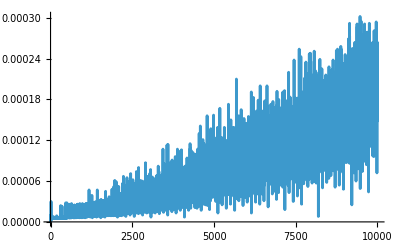

```mathematica
ListLinePlot[Table[First[Timing[n^n]], {n, 10000}]]
```

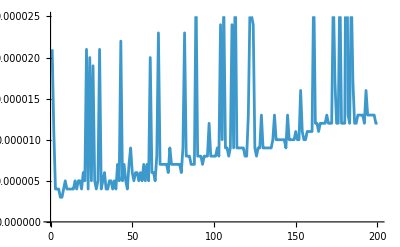

```mathematica
ListLinePlot[Table[First[Timing[Sort[RandomSample[Range[n],n]]]],{n,200}]]
```

```mathematica
Counts[If[StringLength[#]>2,StringTake[#, 2],Nothing]&/@WordList[]]
```

<|aa→2,ab→170,ac→217,ad→190,ae→26,af→72,ag→81,ah→4,ai→55,AI→1,aj→1,ak→2,al→204,am→138,an→329,ao→3,ap→165,Ap→1,aq→14,ar→207,as→197,AS→1,at→98,au→117,Au→1,av→46,aw→30,ax→11,ay→2,az→4,ba→448,BA→1,be→358,bi→208,bl→254,bo→302,br→306,bu→255,by→13,ca→612,ce→126,ch→442,ci→89,cl→265,cn→1,co→1589,CO→1,cr→337,cu→184,cy→45,cz→3,da→152,de→884,De→1,dh→2,di→827,DN→1,do→243,DO→1,dr→172,du→113,dw→9,dy→29,ea→72,eb→7,ec→45,ed→39,ee→4,e'→2,ef→45,eg→28,ei→16,ej→3,el→136,em→143,en→315,eo→1,ep→53,eq→41,er→55,es→63,et→42,eu→25,ev→76,ew→2,ex→415,ey→21,fa→275,fe→174,Fe→1,fi→251,fj→1,fl→266,fo→335,FO→1,fr→228,Fr→1,fu→138,ga→193,ge→153,gh→15,gi→65,gl→136,gn→13,go→123,Go→1,gr→347,gu→120,gy→19,ha→362,he→320,hi→126,HI→1,h'→1,ho→339,hu→134,hy→116,ia→4,ib→4,ic→27,id→54,if→1,ig→18,il→54,im→324,in→1243,io→10,ip→1,ir→90,is→35,it→16,iv→3,ja→72,Ja→1,je→47,ji→32,jo→76,ju→86,Ju→2,ka→20,ke→40,kh→3,kH→1,ki→88,kl→4,kn→51,ko→10,kp→1,kr→5,ku→3,kv→1,la→300,le→224,li→293,ll→2,lo→225,lu→102,ly→20,ma→588,Ma→2,me→362,mi→408,mn→2,mo→392,Mo→1,mu→205,my→32,na→129,ne→208,ni→87,no→303,No→1,nt→1,nu→85,ny→4,oa→15,ob→126,oc→46,o'→2,Oc→1,od→19,oe→2,of→46,og→3,oh→4,oi→12,ok→3,ol→20,om→19,on→33,oo→7,op→86,or→114,os→28,ot→7,ou→125,ov→215,ow→10,ox→18,oy→1,oz→1,pa→552,pe→487,pf→1,ph→160,pi→216,pl→228,pn→4,po→402,pr→815,ps→50,pt→3,pu→225,py→22,qu→194,ra→307,re→1227,rh→39,ri→148,ro→206,ru→122,ry→1,sa→321,Sa→1,sc→334,se→552,Se→1,sh→376,si→241,sk→94,sl→196,sm→77,sn→115,so→299,sp→400,sq→56,st→697,su→519,Su→1,sv→1,sw→119,sy→100,ta→269,te→313,th→283,Th→1,ti→166,TN→1,to→252,tr→476,ts→3,tu→119,Tu→1,tw→49,ty→42,ub→2,ud→1,UF→1,ug→3,uk→2,ul→24,um→13,un→1335,UN→1,up→74,ur→36,us→24,ut→18,uv→2,ux→1,va→143,ve→170,vi→214,VI→1,vo→84,vu→15,wa→252,we→126,We→1,wh→165,wi→186,wo→166,wr→68,xe→6,xy→3,ya→25,ye→35,yi→6,yo→27,yt→2,yu→7,za→3,ze→19,zi→15,zl→1,zo→13,zu→1,zw→1,zy→3|>

```mathematica
Reap[Fold[10 Sow[#1] + #2 &,{1,2,3,4,5}]]
```

{12345,{{1,12,123,1234}}}

```mathematica
Last[Reap[Nest[If[EvenQ[#], Sow[#/2], 3#+1]&, 1000, 20]]]
```

{{500,250,125,188,94,47,71,107,161,242,121,182,91}}